```mathematica
FunctE[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))+((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
FunctE1[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]
```

-Im[(z1^2+(ⅈ gamma12 omega z1 z2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2+(gamma12^2 omega^2)/(ⅈ (gamma12+gamma2) omega-omega^2+omega2^2))]

```mathematica
FunctE2[omega_,omega1_,omega2_,gamma1_,gamma2_,gamma12_,z1_,z2_]=-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]
```

-Im[((ⅈ gamma12 omega z1 z2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+z2^2)/(ⅈ (gamma12+gamma2) omega-omega^2+(gamma12^2 omega^2)/(ⅈ (gamma1+gamma12) omega-omega^2+omega1^2)+omega2^2)]

```mathematica
GammaSMLO[omega_,gammarx_,omegarx_]=gammarx*omega/omegarx
```

(gammarx omega)/omegarx

```mathematica
MainDirecroty=NotebookDirectory[]
```

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\

```mathematica
Filename="group_pt_78_196.dat";
DataExp=ReadList[FileNameJoin[{MainDirecroty,Filename}],Number];
Ncolumbs=3;
Nmaxpoints1=Length[DataExp]/Ncolumbs-1;
X1aver=Table[DataExp[[Ncolumbs*i+1]],{i,0,Nmaxpoints1}];
Y1aver=Table[DataExp[[Ncolumbs*i+2]],{i,0,Nmaxpoints1}];
dY1aver=Table[DataExp[[Ncolumbs*i+3]],{i,0,Nmaxpoints1}];
Clear[DataExp]
```

```mathematica
Needs["ErrorBarPlots`"]
```

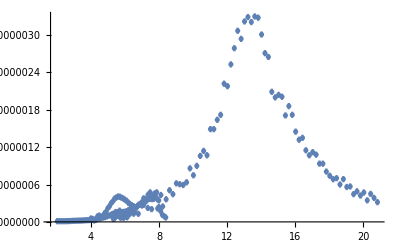

```mathematica
ErrorListPlot[{Transpose[{X1aver,Y1aver,dY1aver}]},PlotRange->All]
```

```mathematica
(* Fit  the cross section in the region [Ulow,Uupper] *)
```

```mathematica
Ulow=0.0;
Uupper=25.0;
Nlow=1;
Nupper=Length[Y1aver]
Do[If[X1aver[[i]]<Ulow,Nlow=i,Nlow=Nlow],{i,1,Length[Y1aver]}];
Do[If[X1aver[[i]]<Uupper,Nupper=i,Nupper=Nupper],{i,1,Length[Y1aver]}];
Nlow
Nupper
```

206

1

206

```mathematica
1
```

1

```mathematica
(*X1aver*)
```

```mathematica
(*Y1aver*)
```

```mathematica
(*dY1aver*)
```

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.0000564207+((0.+«23» ⅈ) omega)/(«1»))/(282.824+«3»+(0.209547 («5»)^2)/(176.679+«1»-«1»))+(«22»+(«1»)/(«1»))/(«19»+«1»-«1»+(«1»)/(«1»))]]

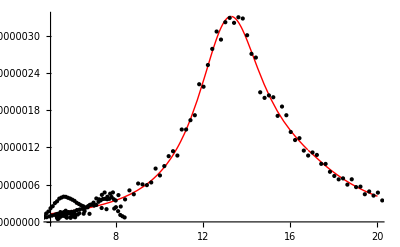

16.8174

13.2921

6.04751

3.22818

0.457763

0.00751137

0.0120012

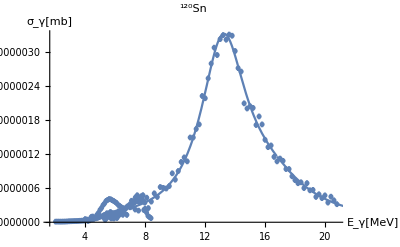

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 16.8174 | 0.77086 | 21.8164 | 1.122×10^-54
omega2p | 13.2921 | 0.0970559 | 136.953 | 7.18785×10^-199
Gamma1p | 6.04751 | 1.22619 | 4.93195 | 1.71405×10^-6
Gamma2p | 3.22818 | 0.396241 | 8.14701 | 4.06127×10^-14
Gamma12p | 0.457763 | 0.486144 | 0.941622 | 0.347528
Z10 | 0.00751137 | 0.00137847 | 5.44908 | 1.48643×10^-7
Z20 | 0.0120012 | 0.000667414 | 17.9816 | 1.42734×10^-43

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{16.8174,0.77086,21.8164,1.122×10^-54},{13.2921,0.0970559,136.953,7.18785×10^-199},{6.04751,1.22619,4.93195,1.71405×10^-6},{3.22818,0.396241,8.14701,4.06127×10^-14},{0.457763,0.486144,0.941622,0.347528},{0.00751137,0.00137847,5.44908,1.48643×10^-7},{0.0120012,0.000667414,17.9816,1.42734×10^-43}}

3.6596

3.6596

```mathematica
(*TSE  !!!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,Nlow,Nmaxpointstemp}];
FordY1aver=Table[dY1aver[[i]],{i,Nlow,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,Nlow,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0,13<omega1p < 20, 7<omega2p<15, 3<Gamma1p<8, 1<Gamma2p<6, 0<Gamma12p<12 (*, Z10<10, Z20<10*)
},{{omega1p,12},{omega2p,7},{Gamma1p,3},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","120"],"Sn"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.000144578/(178.287+(0.+3.57297 ⅈ) omega-omega^2)+0.000055712/(270.174+«1»-omega^2)]]

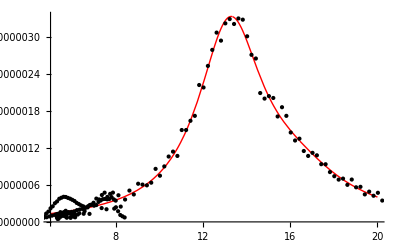

13.3524

16.437

3.57297

5.67319

0.0120241

0.00746404

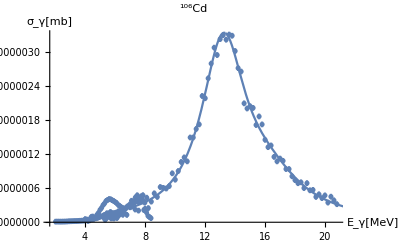

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 13.3524 | 0.0604074 | 221.04 | 6.07246×10^-241
omega2p | 16.437 | 0.487846 | 33.6929 | 2.15592×10^-84
Gamma1p | 3.57297 | 0.168207 | 21.2415 | 3.63952×10^-53
Gamma2p | 5.67319 | 0.966339 | 5.87081 | 1.78019×10^-8
Z10 | 0.0120241 | 0.000579604 | 20.7453 | 9.46942×10^-52
Z20 | 0.00746404 | 0.00116788 | 6.39112 | 1.13553×10^-9

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{13.3524,0.0604074,221.04,6.07246×10^-241},{16.437,0.487846,33.6929,2.15592×10^-84},{3.57297,0.168207,21.2415,3.63952×10^-53},{5.67319,0.966339,5.87081,1.78019×10^-8},{0.0120241,0.000579604,20.7453,9.46942×10^-52},{0.00746404,0.00116788,6.39112,1.13553×10^-9}}

3.65495

3.65495

```mathematica
(*independent Gamma12p=0 !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0, 10<omega1p < 20 },{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEgam0[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEgam0=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.00021177+((0.+«22» ⅈ) omega)/(«1»))/(194.976+«1»-«1»+(10.0003 («5»)^2)/(160.712+«1»-«1»))+(«22»+(«1»)/(«1»))/(«19»+«1»-«1»+(«1»)/(«1»))]]

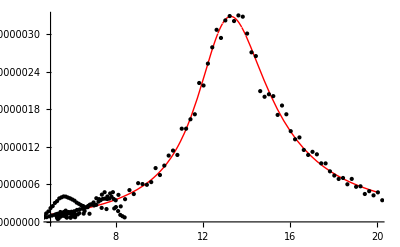

12.6772

13.9634

3.62587

4.00678

3.16233

0.00262805

0.0145523

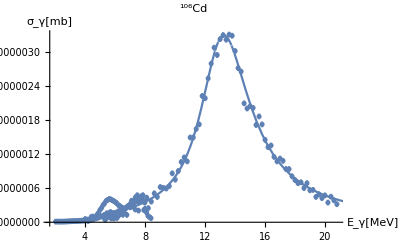

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 12.6772 | 0.605915 | 20.9224 | 3.74485×10^-52
omega2p | 13.9634 | 0.181528 | 76.9214 | 5.52211×10^-150
Gamma1p | 3.62587 | 0.842715 | 4.30261 | 0.0000264514
Gamma2p | 4.00678 | 0.892856 | 4.4876 | 0.0000121747
Gamma12p | 3.16233 | 1.96562 | 1.60882 | 0.109242
Z10 | 0.00262805 | 0.00272941 | 0.962861 | 0.336786
Z20 | 0.0145523 | 0.000274808 | 52.9545 | 3.04275×10^-119

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{12.6772,0.605915,20.9224,3.74485×10^-52},{13.9634,0.181528,76.9214,5.52211×10^-150},{3.62587,0.842715,4.30261,0.0000264514},{4.00678,0.892856,4.4876,0.0000121747},{3.16233,1.96562,1.60882,0.109242},{0.00262805,0.00272941,0.962861,0.336786},{0.0145523,0.000274808,52.9545,3.04275×10^-119}}

3.75413

3.75413

```mathematica
(*TSE SMLO GDR and PDR *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,3},{Gamma2p,2},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.000119224+((0.+«23» ⅈ) omega)/(216.067+«1»«1»«1»))/(180.37+«3»+(2.16824×10^-11 «1»)/(216.067+«1»-(«5»)^2))+(«1»«1»«1»)/(«1»)]]

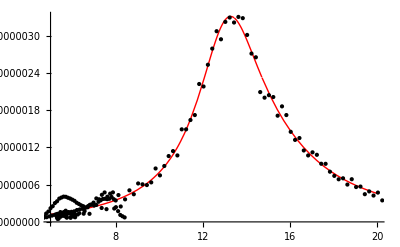

13.4302

14.6992

3.58512

7.47867

4.65643×10^-6

0.010919

0.00955693

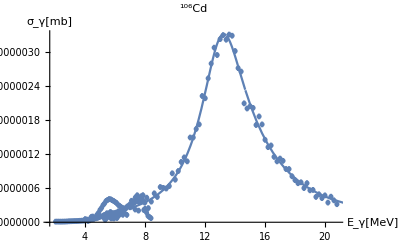

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 13.4302 | 0.146957 | 91.3885 | 1.81128×10^-164
omega2p | 14.6992 | 0.431889 | 34.0347 | 6.58775×10^-85
Gamma1p | 3.58512 | 0.781644 | 4.58664 | 7.95689×10^-6
Gamma2p | 7.47867 | 1.33938 | 5.58369 | 7.65306×10^-8
Gamma12p | 4.65643×10^-6 | 1.08377 | 4.29653×10^-6 | 0.999997
Z10 | 0.010919 | 0.000953008 | 11.4574 | 1.14121×10^-23
Z20 | 0.00955693 | 0.000999724 | 9.55958 | 4.65918×10^-18

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{13.4302,0.146957,91.3885,1.81128×10^-164},{14.6992,0.431889,34.0347,6.58775×10^-85},{3.58512,0.781644,4.58664,7.95689×10^-6},{7.47867,1.33938,5.58369,7.65306×10^-8},{4.65643×10^-6,1.08377,4.29653×10^-6,0.999997},{0.010919,0.000953008,11.4574,1.14121×10^-23},{0.00955693,0.000999724,9.55958,4.65918×10^-18}}

3.68394

3.68394

```mathematica
(*TSE SMLO GDR and PDG G=const !!!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,omega1p>0,omega2p>0,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(0.00133417+((0.+«21» ⅈ) omega)/(167.181+«1»«1»«1»))/(965.526-(«5»)^2+«1»+(866.009 («5»)^2)/(167.181+«1»-(«5»)^2))+(«1»)/(«1»)]]

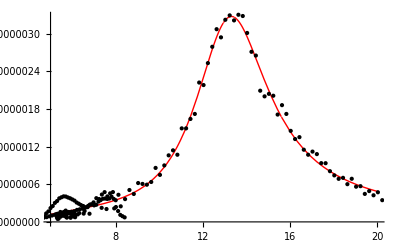

12.9298

31.0729

-21.2222

442.722

29.428

0.00866135

0.0365263

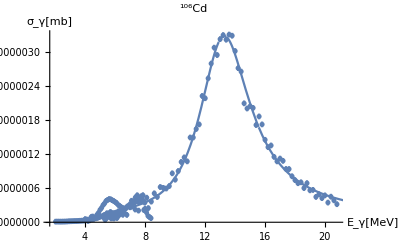

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 12.9298 | 0.133546 | 96.8197 | 2.38702×10^-169
omega2p | 31.0729 | 15.0951 | 2.05848 | 0.0408472
Gamma1p | -21.2222 | 18.8601 | -1.12525 | 0.26184
Gamma2p | 442.722 | 782.927 | 0.565471 | 0.57239
Gamma12p | 29.428 | 19.4324 | 1.51438 | 0.131516
Z10 | 0.00866135 | 0.000441867 | 19.6017 | 2.37918×10^-48
Z20 | 0.0365263 | 0.0209814 | 1.74089 | 0.0832477

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{12.9298,0.133546,96.8197,2.38702×10^-169},{31.0729,15.0951,2.05848,0.0408472},{-21.2222,18.8601,-1.12525,0.26184},{442.722,782.927,0.565471,0.57239},{29.428,19.4324,1.51438,0.131516},{0.00866135,0.000441867,19.6017,2.37918×10^-48},{0.0365263,0.0209814,1.74089,0.0832477}}

3.71862

3.71862

```mathematica
(*TSE SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],Gamma12p,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Gamma12p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Gamma12p,0.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Gamma12p/.FITtemp["BestFitParameters"]
Par6=Z10/.FITtemp["BestFitParameters"]
Par7=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncTSEPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Gamma12p-> Par5,Z10-> Par6,Z20-> Par7};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2TSEPDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-7)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-7)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.000205415/(187.632-(1.-0.353782 ⅈ) omega^2)+(9.99643×10^9)/(9.6962×10^9-(«1») («5»)^2)]]

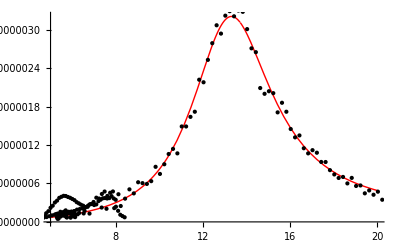

13.6979

98469.3

4.84606

99847.1

0.0143323

99982.2

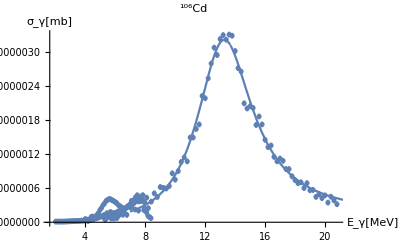

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 13.6979 | 0.038158 | 358.977 | 5.93616×10^-283
omega2p | 98469.3 | 16569.9 | 5.94267 | 1.2282×10^-8
Gamma1p | 4.84606 | 0.131359 | 36.8917 | 3.49174×10^-91
Gamma2p | 99847.1 | 3268.24 | 30.5507 | 2.87977×10^-77
Z10 | 0.0143323 | 0.000191777 | 74.7344 | 4.25969×10^-148
Z20 | 99982.2 | 6527.65 | 15.3167 | 1.50255×10^-35

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{13.6979,0.038158,358.977,5.93616×10^-283},{98469.3,16569.9,5.94267,1.2282×10^-8},{4.84606,0.131359,36.8917,3.49174×10^-91},{99847.1,3268.24,30.5507,2.87977×10^-77},{0.0143323,0.000191777,74.7344,4.25969×10^-148},{99982.2,6527.65,15.3167,1.50255×10^-35}}

4.79572

4.79572

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[(9.99567×10^9)/(3.36738×10^11+(0.+99997.4 ⅈ) omega-omega^2)+0.000183642/(185.586-(1.-«1») «1»)]]

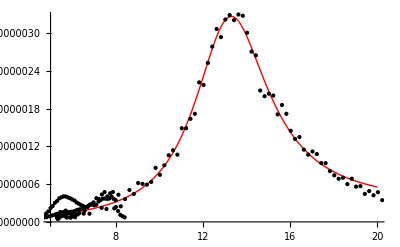

13.623

580291.

4.38543

99997.4

0.0135514

99978.3

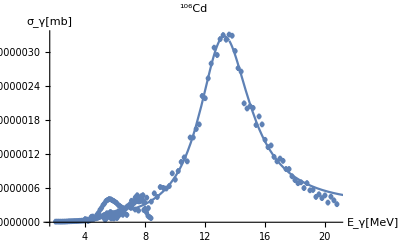

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 13.623 | 0.0306343 | 444.698 | 1.57449×10^-301
omega2p | 580291. | 2257.06 | 257.1 | 5.04512×10^-254
Gamma1p | 4.38543 | 0.121954 | 35.9597 | 2.99139×10^-89
Gamma2p | 99997.4 | 3274.47 | 30.5385 | 3.07562×10^-77
Z10 | 0.0135514 | 0.000185453 | 73.072 | 3.27027×10^-146
Z20 | 99978.3 | 6550.19 | 15.2634 | 2.19096×10^-35

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{{13.623,0.0306343,444.698,1.57449×10^-301},{580291.,2257.06,257.1,5.04512×10^-254},{4.38543,0.121954,35.9597,2.99139×10^-89},{99997.4,3274.47,30.5385,3.07562×10^-77},{0.0135514,0.000185453,73.072,3.27027×10^-146},{99978.3,6550.19,15.2634,2.19096×10^-35}}

4.23629

4.23629

```mathematica
(*independent Gamma12p=0, SMLO GDR and PDG G=const !!!!!*)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,GammaSMLO[omega,Gamma1p,omega1p],Gamma2p,0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1.},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRconsGDRsmlo[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRconsGDRsmlo=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8,5.×10^-8}

FittedModel[-Im[0.000191132/(186.808+(0.+4.32504 ⅈ) omega-omega^2)+57908.6/(7.87588×10^9-(1.-«1») «1»)]]

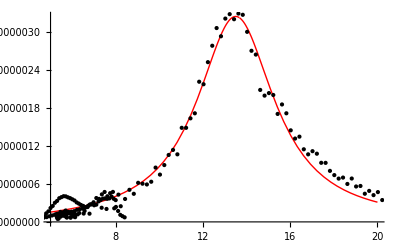

13.6678

88746.2

4.32504

457386.

0.013825

240.642

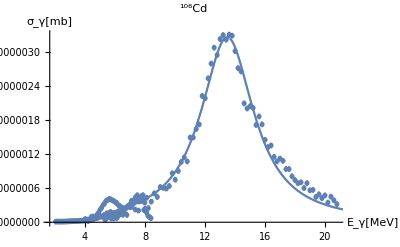

C:\Users\beeff\go\src\github.com\orsenkucher\f1\cd106\FigSigmaFit106Cd.eps

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-772.198] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
omega1p | 13.6678 | 0.032393 | 421.936 | 5.70188×10^-297
omega2p | 88746.2 | 17788.4 | 4.98898 | 1.31531×10^-6
Gamma1p | 4.32504 | 0.0947137 | 45.6643 | 9.56218×10^-108
Gamma2p | 457386. | 690.727 | 662.181 | 0.
Z10 | 0.013825 | 0.000151491 | 91.2597 | 5.92377×10^-165
Z20 | 240.642 | 2.62379×10^6 | 0.0000917156 | 0.999927

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::munfl: Exp[-772.198] is too small to represent as a normalized machine number; precision may be lost.

{{13.6678,0.032393,421.936,5.70188×10^-297},{88746.2,17788.4,4.98898,1.31531×10^-6},{4.32504,0.0947137,45.6643,9.56218×10^-108},{457386.,690.727,662.181,0.},{0.013825,0.000151491,91.2597,5.92377×10^-165},{240.642,2.62379×10^6,0.0000917156,0.999927}}

6.08515

6.08515

```mathematica
(*independent Gamma12p=0, SMLO PDR and GDR G=const *)
Nmaxpointstemp=Nupper;
FordY1aver=Table[1,{i,1,Nmaxpointstemp}]
FordY1aver=Table[dY1aver[[i]],{i,1,Nmaxpointstemp}]
Data1=Table[{X1aver[[i]],Y1aver[[i]]},{i,1,Nmaxpointstemp}];
Data2plotSn130=Table[{X1aver[[i]],Y1aver[[i]],dY1aver[[i]]},{i,1,Nmaxpointstemp}];
model=FunctE[omega,omega1p,omega2p,Gamma1p,GammaSMLO[omega,Gamma2p,omega2p],0,Z10,Z20];
FITtemp=NonlinearModelFit[Data1,{model,Gamma2p>0,Z20>0,Z10>0},{{omega1p,16},{omega2p,7},{Gamma1p,6},{Gamma2p,1},{Z10,0.001},{Z20,0.1*0.001}}, omega,Weights->1/FordY1aver^2]
Plot[FITtemp[x],{x,5,20},Epilog:>Point[Data1],PlotStyle->{Red,Thick}]
Par1=omega1p/.FITtemp["BestFitParameters"]
Par2=omega2p/.FITtemp["BestFitParameters"]
Par3=Gamma1p/.FITtemp["BestFitParameters"]
Par4=Gamma2p/.FITtemp["BestFitParameters"]
Par5=Z10/.FITtemp["BestFitParameters"]
Par6=Z20/.FITtemp["BestFitParameters"]
Filename="FigSigmaFit106Cd.eps";
ResponseFuncPDRsmloGDRcons[omega_]=model/.{omega1p-> Par1 ,omega2p-> Par2,Gamma1p-> Par3,Gamma2p-> Par4,Z10-> Par5,Z20-> Par6};
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[FITtemp[x],{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
Export[FileNameJoin[{MainDirecroty,Filename}],%]
FITtemp["ParameterTable"]
vals=FITtemp["ParameterTableEntries"]
Chi2PDRsmloGDRcons=Sum[(FITtemp["FitResiduals"][[i]]/FordY1aver[[i]])^2,{i,1,Length[FITtemp["FitResiduals"]]}]/(Nmaxpointstemp+1-6)
Sum[((Data1[[i,2]]-FITtemp[Data1[[i,1]]])/FordY1aver[[i]])^2,{i,1,Length[FordY1aver]}]/(Nmaxpointstemp+1-6)
FITtemp1[x_]=FITtemp[x];
```

```mathematica
"E:\\Sasha\\work\\Students\\Kucher\\Cd106\\FigSigmaFit106Cd.eps"
```

E:\Sasha\work\Students\Kucher\Cd106\FigSigmaFit106Cd.eps

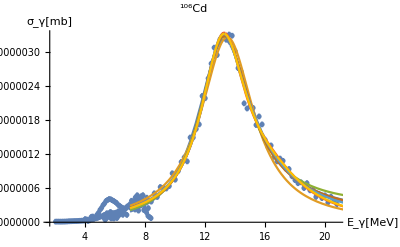

```mathematica
Show[ErrorListPlot[Data2plotSn130,PlotRange->All,PlotLabel->Style[Row[{Superscript["","106"],"Cd"}],FontFamily->"Times",18,Bold],AxesLabel->{Style[Row[{Subscript["E","γ"],"[MeV]"}],FontFamily->"Times",12,Italic],Style[Row[{Subscript["σ","γ"],"[mb]",""}],FontFamily->"Times",12,Italic]}],Plot[{ResponseFuncPDRsmloGDRsmlo[x],ResponseFuncPDRsmloGDRcons[x],ResponseFuncPDRconsGDRsmlo[x],ResponseFuncTSEgam0[x],ResponseFuncTSEPDRsmloGDRsmlo[x],ResponseFuncTSEPDRsmloGDRcons[x],ResponseFuncTSEPDRconsGDRsmlo[x],ResponseFuncTSEgam[x]},{x,7,25},PlotRange->All,PlotStyle->{PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium],PointSize[Medium]}]]
```

```mathematica
Chi2PDRsmloGDRsmlo
Chi2PDRsmloGDRcons
Chi2PDRconsGDRsmlo
Chi2TSEgam0
Chi2TSEPDRsmloGDRsmlo
Chi2TSEPDRsmloGDRcons
Chi2TSEPDRconsGDRsmlo
Chi2TSEgam
```

4.79572

6.08515

4.23629

3.65495

3.75413

3.71862

3.68394

3.6596